```mathematica
Needs["dsvsolve`"];
```

## Input

Edit or simply evaluate the following cell to see the input

General::compat: Combinatorica Graph and Permutations functionality has been superseded by preloaded functionality. The package now being loaded may conflict with this. Please see the Compatibility Guide for details.

SetDelayed::write: Tag Element in a_List∈{index___} is Protected.

dSVtShowInput::assm: Assumptions made: {b→0.75,Mt→0.94,s→0.08}.

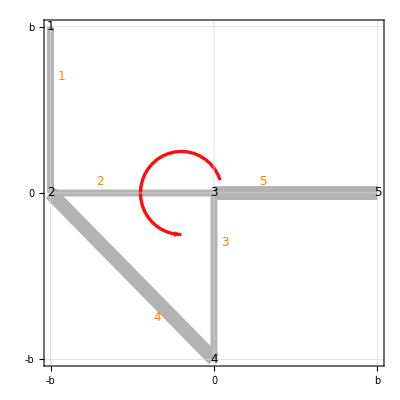

```mathematica
example={$$nodes->{{-b, b}, {-b, 0}, {0, 0}, {0, -b}, {b, 0}},
$$edges->{{1, 2}, {2, 3}, {3, 4}, {4, 2}, {3, 5}},
$$thicknesses->{s,s,s,2s,2s},$$absname->t,$$thname->z,
$$traction->0,$$wheretraction->{0, 0},
$$shear->{0, 0}, $$whereshear->{0, 0},
$$bending->{0, 0}, $$torsion->Mt}; dSVtShowInput[example]
```

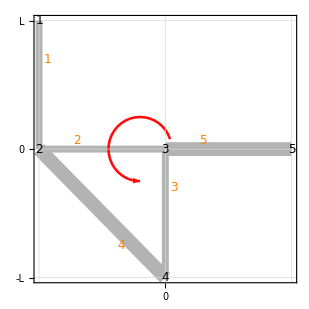

-Graphics-

## Output

Evaluate the following cell to solve the problem and see the output

```mathematica
sol = {AB, rG, JB, CS, FS, KT, sigma, tau, gobj, details} = dSVtSolve[example];
gsol=dSVtShowOutput[example, sol]
```

First::nofirst: {} has zero length and no first element.

Last::nolast: {} has zero length and no last element.

123456

Evaluate the following cell to print the above output

```mathematica
CellPrint/@Rest/@Last[sol];
Print/@Cases[gsol,Graphics[___],Infinity];
```

Numerical assumptions for visualization purposes

{b→0.75,Mt→0.94,s→0.08}

Edge lengths

{{b,b,b,√2 b,b}}

Edges areas Ai

{{b s,b s,b s,2 √2 b s,2 b s}}

Total area A

(5+2 √2) b s

Edges static moments sPi

{{{-b^2 s,(b^2 s)/2},{-(b^2 s)/2,0},{0,-(b^2 s)/2},{-√2 b^2 s,-√2 b^2 s},{b^2 s,0}}}

Static moment sP

{{-1/2 (1+2 √2) b^2 s,-√2 b^2 s}}

Edge centroids Gi

{{{-b,b/2},{-b/2,0},{0,-b/2},{-b/2,-b/2},{b/2,0}}}

Centroid G

{{-(b+2 √2 b)/(10+4 √2),-(√2 b)/(5+2 √2)}}

Edges Euler inertia tensors IPi

{{{{b^3 s,-(b^3 s)/2},{-(b^3 s)/2,(b^3 s)/3}},{{(b^3 s)/3,0},{0,0}},{{0,0},{0,(b^3 s)/3}},{{2/3 √2 b^3 s,1/3 √2 b^3 s},{1/3 √2 b^3 s,2/3 √2 b^3 s}},{{(2 b^3 s)/3,0},{0,0}}}}

Total Euler inertia tensor IP

{{2/3 (3+√2) b^3 s,1/6 (-3+2 √2) b^3 s},{1/6 (-3+2 √2) b^3 s,2/3 (1+√2) b^3 s}}

Inertia tensor after translation in the centroid IG

{{((125+76 √2) b^3 s)/(60+24 √2),((-19+√2) b^3 s)/(6 (5+2 √2))},{((-19+√2) b^3 s)/(6 (5+2 √2)),(2 (6+7 √2) b^3 s)/(15+6 √2)}}

Principal inertia momoments (jI, jII) and associated directions

{{((173+132 √2-√(3 (4179+824 √2))) b^3 s)/(24 (5+2 √2)),{(77+20 √2+√(3 (4179+824 √2)))/(4 (-19+√2)),1}},{((173+132 √2+√(3 (4179+824 √2))) b^3 s)/(24 (5+2 √2)),{(77+20 √2-√(3 (4179+824 √2)))/(4 (-19+√2)),1}}}

Rotation to principal directions

73.1

Radii of gyration (ρI, ρII)

{{(√(1/b) b^(3/2))/(2 (5+2 √2) √(6/(173+132 √2-√(3 (4179+824 √2))))),(√(1/6 (173+132 √2+√(3 (4179+824 √2)))) √(1/b) b^(3/2))/(10+4 √2)}}

Section moduli (WI, WII) and associated directions

{{{-((-19+√2) (173+132 √2-√(3 (4179+824 √2))) b^2 s)/(3 (1103+530 √2+11 √(3 (4179+824 √2))+6 √(6 (4179+824 √2)))),-((-19+√2) (173+132 √2-√(3 (4179+824 √2))) b^2 s)/(3 (1485+750 √2+9 √(3 (4179+824 √2))+2 √(6 (4179+824 √2))))},{(77+20 √2+√(3 (4179+824 √2)))/(4 (-19+√2)),1}},{{((-19+√2) (173+132 √2+√(3 (4179+824 √2))) b^2 s)/(3 (-901-286 √2+√(3 (4179+824 √2))+2 √(6 (4179+824 √2)))),((-19+√2) (173+132 √2+√(3 (4179+824 √2))) b^2 s)/(-45 (99+50 √2)+27 √(3 (4179+824 √2))+6 √(6 (4179+824 √2)))},{(77+20 √2-√(3 (4179+824 √2)))/(4 (-19+√2)),1}}}

Coefficients {a0,a1,a2} for sigma (= a0 + a1 x1 + a2 x2)

{0,0,0}

Sigma in principal axis (ξ,η)

0

Neutral axis for sigma

{}

Intersections of neutral axis with principal axis

{Last[{}],Last[{}]}

Inertia ellipse equation

(60075284+42233156 √2) b^2==3 (8 (5405362+3819043 √2) x1^2+4 (5964639+4233997 √2) x1 x2+(78994221+55871390 √2) x2^2+2 b (6 (2122718+1499191 √2) x1+(17211003+12147098 √2) x2))

Kern (Convex hull (convex hull has been computed on a numerical instance!)

{{-((36757061761+25990975168 √2) b)/(96268871385+68072203776 √2),-((21472500144258869+15183350909111090 √2) b)/(58622691790500585+41452503136084536 √2)},{((7876795457+5569946288 √2) b)/(45290586099+32025610524 √2),-(23 (419448142400801+296594625045618 √2) b)/(39545243808984807+27962710189566696 √2)},{(2 b)/9,b/27},{-(2 (18706895321+13227832118 √2) b)/(63778571793+45098546286 √2),((1723269659465581+1218535954710892 √2) b)/(64112747710608843+45334559037354540 √2)}}

(Shear) Cycles in terms of nodes

{{4,2,3,4}}

(Shear) Cycles in terms of edges

{{4,2,3}}

Associated open graph {nodes, edges} (statically undetermined shear)

{{{-b,b},{-b,0},{0,0},{0,-b},{b,0},{0,-b}},{{1,2},{2,3},{3,4},{6,2},{3,5}}}

Jourawsky shear on the associated open graph (statically undetermined shear)

{0,0,0,0,0}

Cycles connectivity

{{0},{1},{1},{1},{0}}

Congruence for statically undetermined shear, matrix ηij

{{((4+√2) b)/(2 s)}}

Congruence for statically undetermined shear, vector η0i

{0}

Statically undetermined shear solution: Prandtl function values

{0}

Statically undetermined shear solution: shear fluxes

{0,0,0,0,0}

Shear stress if the shear force is placed in the shear center

{0,0,0,0,0}

Shear stiffness matrix

{{-(5 (-1709488626454+1104587089569 √2))/2070693296612,(5 (-2130486127310+1488342746363 √2))/1035346648306},{(5 (-2130486127310+1488342746363 √2))/1035346648306,-(5 (-9327610014614+6518173655591 √2))/1553019972459}}

Shear flexibility matrix

{{(160822727969+54797643969 √2)/74430762875,(3 (37423989005+13006797957 √2))/148861525750},{(3 (37423989005+13006797957 √2))/148861525750,(3 (167685875279+108177646061 √2))/297723051500}}

Shear resultants on edges

{{{0,0},{0,0},{0,0},{0,0},{0,0}}}

Shear resultant

{0,0}

Shear center

{{-((1874168649562+1325178033521 √2) b)/(2936468121320+2076327777130 √2),-(34 (12478834992+8823341623 √2) b)/(5 (293646812132+207632777713 √2))}}

Additional torque due to eccentricity

0

(Torsion) Cycles in terms of nodes

{{4,2,3}}

(Torsion) Cycles in terms of edges

{{4,2,3}}

Statically undetermined torsion, congruence matrix ηij

{{((4+√2) b)/(2 s)}}

Statically undetermined torsion, vector  2Ω

{-b^2}

Solution of the statically undetermined torsion

{-(2 b s)/(4+√2)}

Torsion partition over the cycles  Ji/J

{1}

Shear stress due to torsion

{{-(2 (4+√2) Mt z)/(2 b^3+3 (4+√2) b s^2),-(2 Mt)/(2 b^2 s+3 (4+√2) s^3),-(2 Mt)/(2 b^2 s+3 (4+√2) s^3),-Mt/(2 b^2 s+3 (4+√2) s^3),-(4 (4+√2) Mt z)/(2 b^3+3 (4+√2) b s^2)}}

Torsional inertias Jti

{{{4,2,3},(2 b^3 s)/(4+√2)},{1,(b s^3)/3},{5,(8 b s^3)/3}}

Torsional inertia Jt

(2 b^3 s)/(4+√2)+3 b s^3

-Graphics-

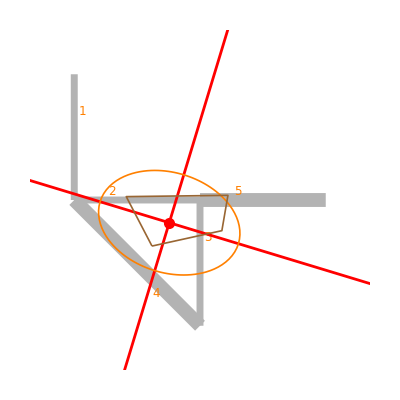

-Graphics-

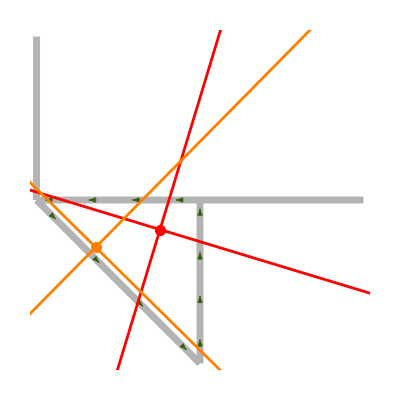

-Graphics-

-Graphics-

```mathematica
Last[sol]
```

{{assums Assunzioni numeriche,Numerical assumptions for visualization purposes,{b→0.75,Mt→0.94,s→0.08}},{edgelengths Lunghezze dei rami,Edge lengths,{{b,b,b,√2 b,b}}},{edgeareas Aree dei rami,Edges areas Ai,{{b s,b s,b s,2 √2 b s,2 b s}}},{totalarea Area totale,Total area A,(5+2 √2) b s},{edgestaticmom Momenti statici dei rami,Edges static moments sPi,{{{-b^2 s,(b^2 s)/2},{-(b^2 s)/2,0},{0,-(b^2 s)/2},{-√2 b^2 s,-√2 b^2 s},{b^2 s,0}}}},{totalstaticmom Momento statico totale,Static moment sP,{{-1/2 (1+2 √2) b^2 s,-√2 b^2 s}}},{edgemasscenters Baricentri dei rami,Edge centroids Gi,{{{-b,b/2},{-b/2,0},{0,-b/2},{-b/2,-b/2},{b/2,0}}}},{totalmasscenter Baricentro,Centroid G,{{-(b+2 √2 b)/(10+4 √2),-(√2 b)/(5+2 √2)}}},{edgeinertias Momenti d'inerzia dei rami,Edges Euler inertia tensors IPi,{{{{b^3 s,-(b^3 s)/2},{-(b^3 s)/2,(b^3 s)/3}},{{(b^3 s)/3,0},{0,0}},{{0,0},{0,(b^3 s)/3}},{{2/3 √2 b^3 s,1/3 √2 b^3 s},{1/3 √2 b^3 s,2/3 √2 b^3 s}},{{(2 b^3 s)/3,0},{0,0}}}}},{totalinertia Momento d'inerzia totale,Total Euler inertia tensor IP,{{2/3 (3+√2) b^3 s,1/6 (-3+2 √2) b^3 s},{1/6 (-3+2 √2) b^3 s,2/3 (1+√2) b^3 s}}},{masscenterinertia Momento d'inerzia dopo translazione nel baricentro,Inertia tensor after translation in the centroid IG,{{((125+76 √2) b^3 s)/(60+24 √2),((-19+√2) b^3 s)/(6 (5+2 √2))},{((-19+√2) b^3 s)/(6 (5+2 √2)),(2 (6+7 √2) b^3 s)/(15+6 √2)}}},{inertiaprinc Momenti e direzioni d'inerzia principali,Principal inertia momoments (jI, jII) and associated directions,{{((173+132 √2-√(3 (4179+824 √2))) b^3 s)/(24 (5+2 √2)),{(77+20 √2+√(3 (4179+824 √2)))/(4 (-19+√2)),1}},{((173+132 √2+√(3 (4179+824 √2))) b^3 s)/(24 (5+2 √2)),{(77+20 √2-√(3 (4179+824 √2)))/(4 (-19+√2)),1}}}},{rotazprinc Rotazione per assi principali d'inerzia,Rotation to principal directions,73.1},{inertiarot rotatori d'inerzia,Radii of gyration (ρI, ρII),{{(√(1/b) b^(3/2))/(2 (5+2 √2) √(6/(173+132 √2-√(3 (4179+824 √2))))),(√(1/6 (173+132 √2+√(3 (4179+824 √2)))) √(1/b) b^(3/2))/(10+4 √2)}}},{sectionmoduli Moduli resistenza a flessione,Section moduli (WI, WII) and associated directions,{{{-((-19+√2) (173+132 √2-√(3 (4179+824 √2))) b^2 s)/(3 (1103+530 √2+11 √(3 (4179+824 √2))+6 √(6 (4179+824 √2)))),-((-19+√2) (173+132 √2-√(3 (4179+824 √2))) b^2 s)/(3 (1485+750 √2+9 √(3 (4179+824 √2))+2 √(6 (4179+824 √2))))},{(77+20 √2+√(3 (4179+824 √2)))/(4 (-19+√2)),1}},{{((-19+√2) (173+132 √2+√(3 (4179+824 √2))) b^2 s)/(3 (-901-286 √2+√(3 (4179+824 √2))+2 √(6 (4179+824 √2)))),((-19+√2) (173+132 √2+√(3 (4179+824 √2))) b^2 s)/(-45 (99+50 √2)+27 √(3 (4179+824 √2))+6 √(6 (4179+824 √2)))},{(77+20 √2-√(3 (4179+824 √2)))/(4 (-19+√2)),1}}}},{sigmacoeff Coefficienti {a0,a1,a2} di sigma,Coefficients {a0,a1,a2} for sigma (= a0 + a1 x1 + a2 x2),{0,0,0}},{sigmaprinc Sigma in assi principali,Sigma in principal axis (ξ,η),0},{neutralaxis Asse neutro sigma,Neutral axis for sigma,{}},{sigma0intprinc Intercette asse neutro con assi principali,Intersections of neutral axis with principal axis,{Last[{}],Last[{}]}},{iellipse Ellisse d'inerzia ,Inertia ellipse equation,(60075284+42233156 √2) b^2==3 (8 (5405362+3819043 √2) x1^2+4 (5964639+4233997 √2) x1 x2+(78994221+55871390 √2) x2^2+2 b (6 (2122718+1499191 √2) x1+(17211003+12147098 √2) x2))},{inertiakernel Nocciolo d'inerzia,Kern (Convex hull (convex hull has been computed on a numerical instance!),{{-((36757061761+25990975168 √2) b)/(96268871385+68072203776 √2),-((21472500144258869+15183350909111090 √2) b)/(58622691790500585+41452503136084536 √2)},{((7876795457+5569946288 √2) b)/(45290586099+32025610524 √2),-(23 (419448142400801+296594625045618 √2) b)/(39545243808984807+27962710189566696 √2)},{(2 b)/9,b/27},{-(2 (18706895321+13227832118 √2) b)/(63778571793+45098546286 √2),((1723269659465581+1218535954710892 √2) b)/(64112747710608843+45334559037354540 √2)}}},{shearcyclesn Cicli,(Shear) Cycles in terms of nodes,{{4,2,3,4}}},{shearcyclese Cicli,(Shear) Cycles in terms of edges,{{4,2,3}}},{opengraph  Sezione principale aperta (problema iperstatico del taglio),Associated open graph {nodes, edges} (statically undetermined shear),{{{-b,b},{-b,0},{0,0},{0,-b},{b,0},{0,-b}},{{1,2},{2,3},{3,4},{6,2},{3,5}}}},{opengraphtension Tensione su sezione aperta (problema iperstatico del taglio),Jourawsky shear on the associated open graph (statically undetermined shear),{0,0,0,0,0}},{cyclesconnectivity Connettivita dei cicli,Cycles connectivity ,{{0},{1},{1},{1},{0}}},{shearcongruencematrix Matrice congruenza (problema iperstatico del taglio),Congruence for statically undetermined shear, matrix ηij ,{{((4+√2) b)/(2 s)}}},{shearcongruencevector Termine noto congruenza (problema iperstatico del taglio),Congruence for statically undetermined shear, vector η0i,{0}},{shearcongruencesol soluzione congruenza (problema iperstatico di taglio),Statically undetermined shear solution: Prandtl function values,{0}},{taucongruencesol Soluzione congruenza (problema iperstatico del taglio),Statically undetermined shear solution: shear fluxes,{0,0,0,0,0}},{jourawskytau Tensione tangenziale dovuta al taglio nel centro di taglio (Jourawsky),Shear stress if the shear force is placed in the shear center,{0,0,0,0,0}},{shearfactors Fattori di rigidezza al taglio,Shear stiffness matrix,{{-(5 (-1709488626454+1104587089569 √2))/2070693296612,(5 (-2130486127310+1488342746363 √2))/1035346648306},{(5 (-2130486127310+1488342746363 √2))/1035346648306,-(5 (-9327610014614+6518173655591 √2))/1553019972459}}},{shearfactorsinv Fattori di flessibilita al taglio,Shear flexibility matrix,{{(160822727969+54797643969 √2)/74430762875,(3 (37423989005+13006797957 √2))/148861525750},{(3 (37423989005+13006797957 √2))/148861525750,(3 (167685875279+108177646061 √2))/297723051500}}},{edgeshearresultants Risultanti taglio sui rami,Shear resultants on edges,{{{0,0},{0,0},{0,0},{0,0},{0,0}}}},{shearresultant Risultante del taglio,Shear resultant,{0,0}},{shearcenter Centro di taglio,Shear center,{{-((1874168649562+1325178033521 √2) b)/(2936468121320+2076327777130 √2),-(34 (12478834992+8823341623 √2) b)/(5 (293646812132+207632777713 √2))}}},{additionaltorque Momento torcente aggiuntivo,Additional torque due to eccentricity,0},{torsioncyclesn Base di cicli in termini di nodi,(Torsion) Cycles in terms of nodes,{{4,2,3}}},{torsioncyclesr Base di cicli in termini di rami,(Torsion) Cycles in terms of edges,{{4,2,3}}},{torsioncongruencematrix Matrice congruenza (problema iperstatico di torsione),Statically undetermined torsion, congruence matrix ηij,{{((4+√2) b)/(2 s)}}},{torsioncongruencevector Termine noto congruenza (problema iperstatico di torsione),Statically undetermined torsion, vector  2Ω,{-b^2}},{torsioncongruencesol soluzione congruenza (problema iperstatico di torsione),Solution of the statically undetermined torsion,{-(2 b s)/(4+√2)}},{torsionpartition ripartizione torsione sui cicli ,Torsion partition over the cycles  Ji/J,{1}},{torsionaltau Tensione tangenziale dovuta alla torsione,Shear stress due to torsion,{{-(2 (4+√2) Mt z)/(2 b^3+3 (4+√2) b s^2),-(2 Mt)/(2 b^2 s+3 (4+√2) s^3),-(2 Mt)/(2 b^2 s+3 (4+√2) s^3),-Mt/(2 b^2 s+3 (4+√2) s^3),-(4 (4+√2) Mt z)/(2 b^3+3 (4+√2) b s^2)}}},{torsionalstiffnesses Singole rigidezze inerzie torsionali (rami, rig),Torsional inertias Jti,{{{4,2,3},(2 b^3 s)/(4+√2)},{1,(b s^3)/3},{5,(8 b s^3)/3}}},{torsionalstiffness Rigidezza Inerzia torsionale,Torsional inertia Jt,(2 b^3 s)/(4+√2)+3 b s^3}}

```mathematica
valori1={b->Quantity[10,"Centimeters"],s->Quantity[0.5,"Centimeters"],z->Quantity[0.5,"Centimeters"],Mt->Quantity[10,"Kilonewtons*Centimeters"],G->Quantity[80,"Gigapascals"],z->s/2};
Last[sol]/.valori1//N
```

{{assums Assunzioni numeriche,Numerical assumptions for visualization purposes,{10. cm→0.75,10. cm kN→0.94,0.5 cm→0.08}},{edgelengths Lunghezze dei rami,Edge lengths,{{10. cm,10. cm,10. cm,14.1421 cm,10. cm}}},{edgeareas Aree dei rami,Edges areas Ai,{{5. cm^2,5. cm^2,5. cm^2,14.1421 cm^2,10. cm^2}}},{totalarea Area totale,Total area A,39.1421 cm^2},{edgestaticmom Momenti statici dei rami,Edges static moments sPi,{{{-50. cm^3,25. cm^3},{-25. cm^3,0.},{0.,-25. cm^3},{-70.7107 cm^3,-70.7107 cm^3},{50. cm^3,0.}}}},{totalstaticmom Momento statico totale,Static moment sP,{{-95.7107 cm^3,-70.7107 cm^3}}},{edgemasscenters Baricentri dei rami,Edge centroids Gi,{{{-10. cm,5. cm},{-5. cm,0.},{0.,-5. cm},{-5. cm,-5. cm},{5. cm,0.}}}},{totalmasscenter Baricentro,Centroid G,{{-2.44521 cm,-1.80651 cm}}},{edgeinertias Momenti d'inerzia dei rami,Edges Euler inertia tensors IPi,{{{{500. cm^4,-250. cm^4},{-250. cm^4,166.667 cm^4}},{{166.667 cm^4,0.},{0.,0.}},{{0.,0.},{0.,166.667 cm^4}},{{471.405 cm^4,235.702 cm^4},{235.702 cm^4,471.405 cm^4}},{{333.333 cm^4,0.},{0.,0.}}}}},{totalinertia Momento d'inerzia totale,Total Euler inertia tensor IP,{{1471.4 cm^4,-14.2977 cm^4},{-14.2977 cm^4,804.738 cm^4}}},{masscenterinertia Momento d'inerzia dopo translazione nel baricentro,Inertia tensor after translation in the centroid IG,{{1237.37 cm^4,-187.2 cm^4},{-187.2 cm^4,676.998 cm^4}}},{inertiaprinc Momenti e direzioni d'inerzia principali,Principal inertia momoments (jI, jII) and associated directions,{{620.215 cm^4,{-3.29677,1.}},{1294.15 cm^4,{0.303327,1.}}}},{rotazprinc Rotazione per assi principali d'inerzia,Rotation to principal directions,73.1},{inertiarot rotatori d'inerzia,Radii of gyration (ρI, ρII),{{3.9806 cm,5.75004 cm}}},{sectionmoduli Moduli resistenza a flessione,Section moduli (WI, WII) and associated directions,{{{15.8127 cm^3,16.8936 cm^3},{-3.29677,1.}},{{173.67 cm^3,136.013 cm^3},{0.303327,1.}}}},{sigmacoeff Coefficienti {a0,a1,a2} di sigma,Coefficients {a0,a1,a2} for sigma (= a0 + a1 x1 + a2 x2),{0.,0.,0.}},{sigmaprinc Sigma in assi principali,Sigma in principal axis (ξ,η),0.},{neutralaxis Asse neutro sigma,Neutral axis for sigma,{}},{sigma0intprinc Intercette asse neutro con assi principali,Intersections of neutral axis with principal axis,{Last[{}],Last[{}]}},{iellipse Ellisse d'inerzia ,Inertia ellipse equation,1.19802×10^10 cm^2==3. (8.64504×10^7 x1^2+4.78097×10^7 x1 x2+1.58008×10^8 x2^2+(2.54574×10^7 x1+3.43896×10^7 x2) (20. cm))},{inertiakernel Nocciolo d'inerzia,Kern (Convex hull (convex hull has been computed on a numerical instance!),{{-3.81816 cm,-3.66283 cm},{1.73919 cm,-2.43956 cm},{2.22222 cm,0.37037 cm},{-5.8662 cm,0.268787 cm}}},{shearcyclesn Cicli,(Shear) Cycles in terms of nodes,{{4.,2.,3.,4.}}},{shearcyclese Cicli,(Shear) Cycles in terms of edges,{{4.,2.,3.}}},{opengraph  Sezione principale aperta (problema iperstatico del taglio),Associated open graph {nodes, edges} (statically undetermined shear),{{{-10. cm,10. cm},{-10. cm,0.},{0.,0.},{0.,-10. cm},{10. cm,0.},{0.,-10. cm}},{{1.,2.},{2.,3.},{3.,4.},{6.,2.},{3.,5.}}}},{opengraphtension Tensione su sezione aperta (problema iperstatico del taglio),Jourawsky shear on the associated open graph (statically undetermined shear),{0.,0.,0.,0.,0.}},{cyclesconnectivity Connettivita dei cicli,Cycles connectivity ,{{0.},{1.},{1.},{1.},{0.}}},{shearcongruencematrix Matrice congruenza (problema iperstatico del taglio),Congruence for statically undetermined shear, matrix ηij ,{{54.1421}}},{shearcongruencevector Termine noto congruenza (problema iperstatico del taglio),Congruence for statically undetermined shear, vector η0i,{0.}},{shearcongruencesol soluzione congruenza (problema iperstatico di taglio),Statically undetermined shear solution: Prandtl function values,{0.}},{taucongruencesol Soluzione congruenza (problema iperstatico del taglio),Statically undetermined shear solution: shear fluxes,{0.,0.,0.,0.,0.}},{jourawskytau Tensione tangenziale dovuta al taglio nel centro di taglio (Jourawsky),Shear stress if the shear force is placed in the shear center,{0.,0.,0.,0.,0.}},{shearfactors Fattori di rigidezza al taglio,Shear stiffness matrix,{{0.355839,-0.123879},{-0.123879,0.352605}}},{shearfactorsinv Fattori di flessibilita al taglio,Shear flexibility matrix,{{3.20188,1.12491},{1.12491,3.23125}}},{edgeshearresultants Risultanti taglio sui rami,Shear resultants on edges,{{{0.,0.},{0.,0.},{0.,0.},{0.,0.},{0.,0.}}}},{shearresultant Risultante del taglio,Shear resultant,{0.,0.}},{shearcenter Centro di taglio,Shear center,{{-6.38235 cm,-2.88969 cm}}},{additionaltorque Momento torcente aggiuntivo,Additional torque due to eccentricity,0.},{torsioncyclesn Base di cicli in termini di nodi,(Torsion) Cycles in terms of nodes,{{4.,2.,3.}}},{torsioncyclesr Base di cicli in termini di rami,(Torsion) Cycles in terms of edges,{{4.,2.,3.}}},{torsioncongruencematrix Matrice congruenza (problema iperstatico di torsione),Statically undetermined torsion, congruence matrix ηij,{{54.1421}}},{torsioncongruencevector Termine noto congruenza (problema iperstatico di torsione),Statically undetermined torsion, vector  2Ω,{-100. cm^2}},{torsioncongruencesol soluzione congruenza (problema iperstatico di torsione),Solution of the statically undetermined torsion,{-1.84699 cm^2}},{torsionpartition ripartizione torsione sui cicli ,Torsion partition over the cycles  Ji/J,{1.}},{torsionaltau Tensione tangenziale dovuta alla torsione,Shear stress due to torsion,{{-0.0265324 kN/cm,-0.19602 kN/cm^2,-0.19602 kN/cm^2,-0.0980101 kN/cm^2,-0.0530647 kN/cm}}},{torsionalstiffnesses Singole rigidezze inerzie torsionali (rami, rig),Torsional inertias Jti,{{{4.,2.,3.},184.699 cm^4},{1.,0.416667 cm^4},{5.,3.33333 cm^4}}},{torsionalstiffness Rigidezza Inerzia torsionale,Torsional inertia Jt,188.449 cm^4}}